```mathematica
k = 5
```

5

```mathematica
range ={-100,100}
```

{-100,100}

```mathematica
NN = RandomInteger[{10,20},k]
```

{20,16,11,19,19}

```mathematica
σ = RandomReal[{10,100}, k]
```

{38.6638,57.4873,72.2535,54.2026,96.7411}

```mathematica
centroids = RandomReal[range,{k,2}]
```

{{25.319,-87.545},{38.256,-74.5788},{-38.5271,-29.0261},{76.5238,58.423},{-61.4788,-84.6538}}

```mathematica
X =Table[
 RandomVariate[MultinormalDistribution[centroids[[i]], DiagonalMatrix[{σ[[i]],σ[[i]]}]],NN[[1]]], {i, 1, k}]
```

{{{45.041,-86.2873},{32.581,-91.7741},{24.6812,-90.3465},{30.9384,-91.6603},{25.6562,-81.9152},{20.5324,-87.5197},{20.43,-85.8846},{26.2443,-81.3125},{26.2468,-86.5086},{22.2544,-96.5861},{27.18,-93.2905},{20.5842,-94.8606},{32.9141,-90.6995},{19.4407,-85.1597},{21.824,-77.9016},{42.693,-91.4365},{28.9161,-80.3354},{14.7474,-83.6189},{22.3904,-78.3072},{25.4208,-93.4831}},{{31.124,-85.1009},{31.3924,-83.0574},{40.7275,-80.2565},{38.7382,-75.0325},{32.7018,-76.3383},{42.8753,-65.7897},{41.5781,-74.5638},{46.8662,-49.7707},{26.1326,-80.3618},{39.9648,-71.5145},{40.277,-85.0763},{42.9276,-76.8993},{32.7557,-69.5034},{21.8787,-82.558},{46.5243,-72.5698},{34.8848,-69.9838},{32.7815,-73.5999},{23.2323,-68.0989},{40.0016,-68.0127},{28.8011,-63.1458}},{{-46.0284,-35.4587},{-30.9554,-35.5812},{-41.7368,-27.0958},{-29.5355,-17.234},{-34.6401,-41.4753},{-46.9684,-21.9614},{-36.9189,-34.7805},{-33.6733,-41.2726},{-53.5122,-20.6591},{-43.5938,-28.1202},{-23.0426,-14.2851},{-45.2797,-19.731},{-31.1641,-40.0626},{-48.2021,-34.3973},{-42.3887,-28.0481},{-26.7098,-28.104},{-39.7113,-15.2179},{-33.7426,-18.012},{-31.6123,-29.9179},{-42.0712,-28.3861}},{{67.3789,47.5653},{83.7031,57.9453},{75.9137,56.5178},{79.0896,59.195},{71.2767,72.3488},{79.4411,48.8884},{74.6761,65.7945},{63.8755,54.6174},{88.7338,62.6692},{72.5359,50.939},{73.3748,50.5502},{74.7225,57.0077},{70.8521,49.3754},{76.2245,52.506},{69.5596,64.8378},{75.5723,60.0815},{80.1672,59.708},{76.994,56.2471},{74.9464,41.074},{68.8684,65.5639}},{{-57.2415,-104.412},{-47.6073,-103.917},{-64.8609,-75.3771},{-55.9568,-83.698},{-46.9304,-81.0967},{-69.3357,-94.2398},{-68.1426,-93.1988},{-67.0588,-80.7009},{-57.0269,-84.6352},{-74.6672,-99.6262},{-52.9255,-86.5215},{-79.6226,-89.9349},{-66.2617,-79.8462},{-79.1539,-73.3713},{-65.7193,-95.7517},{-64.1875,-91.4512},{-62.1612,-86.8363},{-47.5367,-78.9488},{-63.9358,-80.021},{-53.535,-96.0357}}}

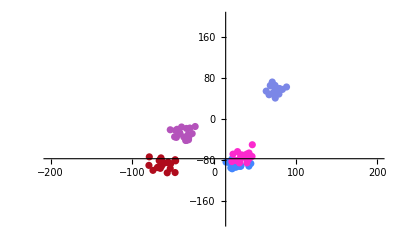

```mathematica
Show[Table[ListPlot[Style[X[[i]], RandomColor[]]],{i,1, k}], PlotRange->{2 range,2 range}]
```

```mathematica
initCentroids =  RandomReal[range,{k,2}]
```

{{-99.5369,5.16074},{-52.2244,-75.4551},{-97.7491,-83.0618},{-69.8787,36.783},{29.1755,29.5529}}

```mathematica
assignCluster[centroids_]:=((Position[#, Min[#]] //Flatten)[[1]]&  @ (Norm /@(centroids- ConstantArray[#, Length[centroids]])))& /@ Flatten[X, 1]
```

```mathematica
calCentroids[clusterassignment_] :=Table[Mean[Flatten[X, 1][[Position[clusterassignment,i]//Flatten]  ]],{i, 1, k}]//fillMissingCentroids
```

```mathematica
fillMissingCentroids[centroids_] := ReplacePart[centroids,Thread[#->RandomReal[range,{Length[#], 2}]]]& @ (Position[centroids,Mean[__]]//Flatten)
```

```mathematica
cluster[centroids_] := cluster[centroids, ConstantArray[{0,0}, Length[centroids]]]
```

```mathematica
cluster[centroids_, prevCentroids_] :=centroids /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] ≤1
```

```mathematica
cluster[centroids_, prevCentroids_] :=cluster[calCentroids[assignCluster[centroids]], centroids]  /; Fold[Plus, 0, Norm /@(prevCentroids-centroids)] >1
```

```mathematica
clusters =cluster[initCentroids]
```

{{-44.9493,-25.9076},{31.172,-80.503},{-62.1934,-87.981},{-31.1995,-30.0725},{74.8953,56.6716}}

```mathematica
clusterAssignment =assignCluster[clusters]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,4,1,4,4,1,4,4,1,1,4,1,4,1,1,4,1,4,4,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

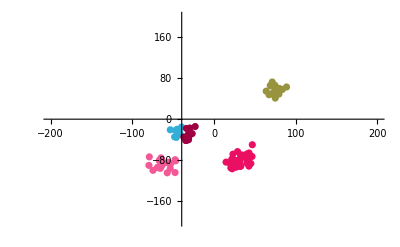

```mathematica
Show[Table[ListPlot[Style[ Flatten[X,1][[Position[clusterAssignment, i]//Flatten]], RandomColor[]]],{i,1,k}],PlotRange->{2 range,2 range}]
```

```mathematica
FindClusters[Flatten[X,1], k]
```

{{{45.041,-86.2873},{32.581,-91.7741},{24.6812,-90.3465},{30.9384,-91.6603},{25.6562,-81.9152},{20.5324,-87.5197},{20.43,-85.8846},{26.2443,-81.3125},{26.2468,-86.5086},{22.2544,-96.5861},{27.18,-93.2905},{20.5842,-94.8606},{32.9141,-90.6995},{19.4407,-85.1597},{21.824,-77.9016},{42.693,-91.4365},{28.9161,-80.3354},{14.7474,-83.6189},{22.3904,-78.3072},{25.4208,-93.4831},{31.124,-85.1009},{31.3924,-83.0574},{40.7275,-80.2565},{38.7382,-75.0325},{32.7018,-76.3383},{42.8753,-65.7897},{41.5781,-74.5638},{26.1326,-80.3618},{39.9648,-71.5145},{40.277,-85.0763},{42.9276,-76.8993},{32.7557,-69.5034},{21.8787,-82.558},{46.5243,-72.5698},{34.8848,-69.9838},{32.7815,-73.5999},{23.2323,-68.0989},{40.0016,-68.0127},{28.8011,-63.1458}},{{46.8662,-49.7707}},{{-46.0284,-35.4587},{-30.9554,-35.5812},{-41.7368,-27.0958},{-29.5355,-17.234},{-34.6401,-41.4753},{-46.9684,-21.9614},{-36.9189,-34.7805},{-33.6733,-41.2726},{-53.5122,-20.6591},{-43.5938,-28.1202},{-23.0426,-14.2851},{-45.2797,-19.731},{-31.1641,-40.0626},{-48.2021,-34.3973},{-42.3887,-28.0481},{-26.7098,-28.104},{-39.7113,-15.2179},{-33.7426,-18.012},{-31.6123,-29.9179},{-42.0712,-28.3861}},{{67.3789,47.5653},{83.7031,57.9453},{75.9137,56.5178},{79.0896,59.195},{71.2767,72.3488},{79.4411,48.8884},{74.6761,65.7945},{63.8755,54.6174},{88.7338,62.6692},{72.5359,50.939},{73.3748,50.5502},{74.7225,57.0077},{70.8521,49.3754},{76.2245,52.506},{69.5596,64.8378},{75.5723,60.0815},{80.1672,59.708},{76.994,56.2471},{74.9464,41.074},{68.8684,65.5639}},{{-57.2415,-104.412},{-47.6073,-103.917},{-64.8609,-75.3771},{-55.9568,-83.698},{-46.9304,-81.0967},{-69.3357,-94.2398},{-68.1426,-93.1988},{-67.0588,-80.7009},{-57.0269,-84.6352},{-74.6672,-99.6262},{-52.9255,-86.5215},{-79.6226,-89.9349},{-66.2617,-79.8462},{-79.1539,-73.3713},{-65.7193,-95.7517},{-64.1875,-91.4512},{-62.1612,-86.8363},{-47.5367,-78.9488},{-63.9358,-80.021},{-53.535,-96.0357}}}

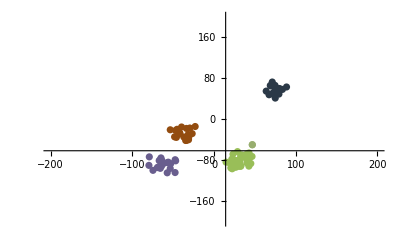

```mathematica
Show[Table[ListPlot[Style[ %[[i]], RandomColor[]]],{i,1,Length[%]}],PlotRange->{2 range,2 range}]
```